# World Map Project

## Data

Landmasses included in triangulation:
sk = Sakhalin
sr = Sri Lanka
hp = Hispaniola
cu = Cuba
c1 = Canadian Arctic 1
c2 = Canadian Arctic 2
c3 = Canadian Arctic 3
c4 = Canadian Arctic 4
c5 = Canadian Arctic 5
c6 = Canadian Arctic 6
c7 = Canadian Arctic 7
p1 = Northern Philippines
p2 = Central Philippines
p3 = Southern Philippines
s1 = Northern Siberian Islands
s2 = Central Siberian Islands
s3 = Southern Siberian Islands
nz = Novaya Zemlya
sv = Svalbard
na = North America
sa = South America
af = Africa
ea = Eurasia
au = Australia
mg = Madagascar
ir = Ireland
gb = Great Britain
ic = Iceland
gn = Greenland
bf = Baffin Island
vc = Victoria Island
el = Ellesmere Island
nf = Newfoundland
bn = Borneo
jv = Java
sm = Sumatra
sl = Sulawesi
ng = New Guinea
zn = New Zealand (North)
zs = New Zealand (South)
tz = Tasmania
hs = Honshu
hk = Hokkaido
an = Antarctica (* In long-lat coordinates, not pixel coordinates *)

```mathematica
anT={{{-58.18611111111111,-63.50277777777779},{-61.51666666666667,-74.85277777777777},{-40.50555555555556,-78.32499999999999},{-14.69444444444445,-71.33055555555555},{17.52777777777778,-69.21388888888887},{53.59166666666667,-65.825},{75.74722222222223,-69.46388888888892},{97.98611111111113,-65.18611111111112},{125.4888888888889,-65.93611111111112},{171.24722222222223,-71.44444444444444},{163.9777777777778,-76.03611111111111},{-160.73055555555555,-78.55000000000001},{-144.54722222222222,-74.97222222222226},{-124.15,-73.47222222222224},{-103.39166666666668,-75.24444444444444},{-102.68333333333335,-71.58333333333333},{-75.82777777777778,-72.36111111111109},{-89.54083647166642,-72.48143747690942},{-118.78789366157639,-82.52778000101745},{149.02096017596392,-70.8359671114568},{-81.83765111842413,-77.93513784643186},{118.04366947923795,-77.41032391645841},{45.875187293116504,-79.7992679588523},{0.,-90}},{{14,15},{15,19},{19,14},{17,21},{21,18},{18,17},{19,13},{13,14},{14,19},{19,15},{15,21},{21,19},{20,10},{10,11},{11,20},{24,22},{22,11},{11,24},{21,3},{3,19},{19,21},{20,22},{22,9},{9,20},{15,16},{16,18},{18,15},{19,12},{12,13},{13,19},{5,6},{6,23},{23,5},{21,17},{17,2},{2,21},{22,20},{20,11},{11,22},{24,11},{11,12},{12,24},{18,21},{21,15},{15,18},{22,8},{8,9},{9,22},{23,6},{6,7},{7,23},{19,3},{3,24},{24,19},{3,4},{4,23},{23,3},{3,23},{23,24},{24,3},{5,23},{23,4},{4,5},{8,22},{22,7},{7,8},{22,23},{23,7},{7,22},{3,21},{21,2},{2,3},{23,22},{22,24},{24,23},{24,12},{12,19},{19,24},{1,2},{2,17},{17,1}},{{14,15,19},{17,21,18},{19,13,14},{19,15,21},{20,10,11},{24,22,11},{21,3,19},{20,22,9},{15,16,18},{19,12,13},{5,6,23},{21,17,2},{22,20,11},{24,11,12},{18,21,15},{22,8,9},{23,6,7},{19,3,24},{3,4,23},{3,23,24},{5,23,4},{8,22,7},{22,23,7},{3,21,2},{23,22,24},{24,12,19},{1,2,17}}};
```

```mathematica
auT={{{1715.,644.5},{1706.4,608.},{1681.2,621.},{1645.2,625.5},{1628.4,630.5},{1604.,599.},{1563.4,585.},{1561.4,560.},{1569.6,516.},{1586.2,508.},{1617.8,520.},{1657.6,528.},{1690.8,511.5},{1718.2,486.},{1753.,492.999},{1773.2,534.},{1773.8,564.},{1736.6,600.},{1589.95,537.008},{1631.98,600.775},{1707.1,575.088},{1689.34,545.759},{1674.22,576.536},{1600.72,566.808},{1660.48,601.475},{1638.57,563.344},{1735.07,539.108},{1685.8,638.5},{1652.8,642.5}},{{10,11},{11,19},{19,10},{27,22},{22,13},{13,27},{10,19},{19,9},{9,10},{8,9},{9,19},{19,8},{21,18},{18,2},{2,21},{11,24},{24,19},{19,11},{2,3},{3,23},{23,2},{8,19},{19,24},{24,8},{20,5},{5,6},{6,20},{7,8},{8,24},{24,7},{26,11},{11,12},{12,26},{24,6},{6,7},{7,24},{4,5},{5,20},{20,4},{25,4},{4,20},{20,25},{26,25},{25,20},{20,26},{21,23},{23,22},{22,21},{15,27},{27,14},{14,15},{26,20},{20,24},{24,26},{15,16},{16,27},{27,15},{3,4},{4,25},{25,3},{11,26},{26,24},{24,11},{27,17},{17,18},{18,27},{25,26},{26,23},{23,25},{12,13},{13,22},{22,12},{21,27},{27,18},{18,21},{18,1},{1,2},{2,18},{13,14},{14,27},{27,13},{22,23},{23,12},{12,22},{22,27},{27,21},{21,22},{6,24},{24,20},{20,6},{23,3},{3,25},{25,23},{17,27},{27,16},{16,17},{12,23},{23,26},{26,12},{2,23},{23,21},{21,2},{3,28},{28,29},{29,4},{3,29}},{{10,11,19},{27,22,13},{10,19,9},{8,9,19},{21,18,2},{11,24,19},{2,3,23},{8,19,24},{20,5,6},{7,8,24},{26,11,12},{24,6,7},{4,5,20},{25,4,20},{26,25,20},{21,23,22},{15,27,14},{26,20,24},{15,16,27},{3,4,25},{11,26,24},{27,17,18},{25,26,23},{12,13,22},{21,27,18},{18,1,2},{13,14,27},{22,23,12},{22,27,21},{6,24,20},{23,3,25},{17,27,16},{12,23,26},{2,23,21},{3,29,28},{3,29,4}}};

tzT={{{1747.2,475.},{1727.6,472.},{1739.2,455.5}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

znT={{{1880.4,510.5},{1890.,472.},{1906.,492.}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

zsT={{{1874.8,474.},{1841.,441.5},{1858.8,435.},{1883.2,463.}},{{1,2},{2,4},{4,1},{2,3},{3,4},{4,2}},{{1,2,4},{2,3,4}}};

eaT={{{1098.8,1162.5},{1061.4,1153.},{1031.6,1123.5},{1013.6,1097.},{986.6,1082.},{997.8,1050.5},{1017.4,1060.5},{1037.8,1037.},{1058.4,1062.},{1051.2,1081.5},{1077.8,1111.5},{1092.4,1104.},{1074.,1089.},{1085.2,1063.5},{1069.4,1029.},{1035.6,1020.5},{1014.98,1024.42},{1018.2,1042.5},{1004.8,1041.},{1003.4,1022.5},{985.4,1016.},{971.,999.},{937.,981.5},{957.,951.},{916.301,948.417},{913.6,909.5},{956.777,911.967},{968.6,935.},{983.594,950.147},{1009.4,955.045},{1042.2,924.5},{1054.18,932.612},{1025.6,961.},{1065.8,938.},{1074.,910.5},{1087.,913.5},{1084.6,930.5},{1100.6,932.5},{1105.41,910.499},{1150.8,907.},{1135.5,872.5},{1169.4,816.5},{1191.6,771.},{1238.4,788.},{1277.71,820.381},{1258.13,841.342},{1235.,835.5},{1215.2,862.5},{1229.8,866.},{1247.,850.5},{1311.8,842.5},{1344.2,811.5},{1371.4,746.},{1385.57,767.749},{1389.4,790.},{1422.8,813.5},{1447.4,817.},{1456.8,787.},{1475.4,784.5},{1480.,747.5},{1511.8,709.},{1508.67,732.03},{1491.,748.5},{1491.4,776.5},{1518.4,748.5},{1540.2,763.5},{1536.,786.},{1519.8,803.5},{1535.,819.5},{1577.,827.5},{1609.4,861.5},{1608.2,888.5},{1594.6,898.},{1600.8,922.},{1621.42,922.073},{1629.2,892.},{1647.4,900.},{1636.8,922.5},{1657.2,946.},{1675.,946.5},{1705.39,983.565},{1718.8,1021.5},{1684.62,1029.47},{1714.2,1057.5},{1779.64,1064.34},{1803.2,1082.5},{1828.4,1081.},{1784.2,1035.5},{1791.2,1001.},{1826.6,1040.5},{1822.,1054.},{1839.88,1069.08},{1866.,1068.5},{1911.2,1086.},{1919.6,1114.5},{1955.,1100.5},{1968.4,1116.5},{1912.4,1146.5},{1860.89,1151.69},{1820.8,1166.5},{1772.6,1169.},{1733.,1187.5},{1703.,1193.},{1694.75,1171.57},{1648.2,1169.},{1656.99,1186.02},{1616.,1194.5},{1560.,1191.5},{1561.6,1219.5},{1509.8,1233.5},{1430.,1206.},{1407.,1191.5},{1338.,1187.71},{1315.2,1166.5},{1321.2,1139.5},{1273.4,1155.5},{1211.8,1130.5},{1200.2,1142.},{1170.4,1106.},{1136.08,1122.46},{1168.2,1118.5},{1175.8,1132.},{1151.6,1147.},{1020,1000},{1217.23,886.245},{1628.47,945.454},{1089.59,955.604},{1361.13,1152.62},{1585.83,873.194},{1665.35,973.066},{1852.09,1092.34},{1561.54,919.34},{1468.82,807.24},{1359.13,775.553},{1636.5,1190.26},{1600.03,950.956},{1506.09,837.352},{1615.75,1161.1},{993.51,997.688},{976.788,973.304},{1258.06,804.191},{1261.75,884.162},{1195.96,923.711},{1818.06,1119.71},{1429.83,852.31},{1382.84,838.522},{1129.9,960.643},{1566.49,853.231},{1000.9,975.4},{1470.19,846.073},{1215.99,810.268},{1240.38,904.298},{1553.18,885.475},{1496.92,805.051},{1458,1142},{1275,1050},{1056.08,986.468},{1883.83,1109.55},{1622.54,991.049},{1281.4,926.422},{1606.31,1107.24},{1576.62,1155.66},{1765.99,1104.97},{1299.18,878.227},{1123.4,1027.69},{1180.15,880.776},{1506.34,915.005},{1359.31,879.383},{1471.06,889.565},{1521.42,872.324},{1348,973},{1406.44,1119.03},{1729.98,1140.87},{1646.11,1064.29},{1448,1043},{1096.24,996.457},{1528.74,1130.24},{1355,1060},{1524.78,971.292},{1244.04,982.474},{1113.31,1082.92},{1656.97,1132.59},{1551,1045},{1206.7,1046.79},{1497.72,1183.32},{1438,945}},{{48,166},{166,42},{42,48},{98,158},{158,95},{95,98},{20,21},{21,139},{139,20},{44,151},{151,43},{43,44},{143,125},{125,152},{152,143},{151,48},{48,42},{42,151},{125,166},{166,48},{48,125},{48,49},{49,125},{125,48},{185,111},{111,155},{155,185},{142,164},{164,160},{160,142},{22,140},{140,139},{139,22},{70,148},{148,69},{69,70},{14,165},{165,181},{181,14},{38,127},{127,37},{37,38},{71,148},{148,70},{70,71},{37,127},{127,34},{34,37},{143,166},{166,125},{125,143},{153,132},{132,167},{167,153},{56,57},{57,145},{145,56},{143,40},{40,166},{166,143},{55,52},{52,134},{134,55},{142,160},{160,152},{152,142},{156,178},{178,115},{115,156},{54,134},{134,53},{53,54},{176,165},{165,15},{15,176},{145,168},{168,146},{146,145},{105,135},{135,138},{138,105},{132,73},{73,74},{74,132},{126,130},{130,159},{159,126},{46,47},{47,141},{141,46},{84,173},{173,182},{182,84},{144,99},{99,100},{100,144},{141,45},{45,46},{46,141},{164,50},{50,51},{51,164},{55,146},{146,52},{52,55},{141,151},{151,44},{44,141},{168,51},{51,52},{52,168},{49,142},{142,152},{152,49},{24,29},{29,140},{140,24},{147,40},{40,143},{143,147},{29,149},{149,140},{140,29},{22,23},{23,140},{140,22},{124,20},{20,139},{139,124},{124,139},{139,149},{149,124},{124,149},{149,33},{33,124},{165,147},{147,184},{184,165},{151,141},{141,47},{47,151},{29,30},{30,149},{149,29},{64,154},{154,59},{59,64},{33,157},{157,124},{124,33},{124,157},{157,16},{16,124},{130,83},{83,159},{159,130},{17,124},{124,16},{16,17},{153,129},{129,73},{73,153},{157,34},{34,127},{127,157},{40,41},{41,166},{166,40},{165,119},{119,181},{181,165},{40,147},{147,38},{38,40},{14,181},{181,13},{13,14},{12,13},{13,181},{181,12},{14,15},{15,165},{165,14},{174,83},{83,84},{84,174},{165,176},{176,147},{147,165},{170,69},{69,148},{148,170},{178,172},{172,128},{128,178},{156,116},{116,117},{117,156},{115,128},{128,114},{114,115},{12,181},{181,120},{120,12},{114,128},{128,113},{113,114},{157,176},{176,15},{15,157},{152,125},{125,49},{49,152},{147,143},{143,180},{180,147},{127,38},{38,147},{147,127},{138,107},{107,162},{162,138},{180,184},{184,147},{147,180},{99,131},{131,158},{158,99},{56,146},{146,55},{55,56},{168,164},{164,51},{51,168},{159,136},{136,126},{126,159},{161,162},{162,177},{177,161},{154,137},{137,133},{133,154},{43,151},{151,42},{42,43},{85,86},{86,163},{163,85},{137,154},{154,68},{68,137},{34,157},{157,33},{33,34},{68,154},{154,64},{64,68},{137,150},{150,133},{133,137},{133,59},{59,154},{154,133},{130,79},{79,80},{80,130},{129,71},{71,72},{72,129},{136,132},{132,74},{74,136},{129,148},{148,71},{71,129},{48,151},{151,47},{47,48},{170,150},{150,137},{137,170},{161,138},{138,162},{162,161},{129,153},{153,148},{148,129},{107,108},{108,162},{162,107},{72,73},{73,129},{129,72},{78,79},{79,126},{126,78},{158,93},{93,94},{94,158},{55,134},{134,54},{54,55},{136,75},{75,126},{126,136},{22,139},{139,21},{21,22},{59,133},{133,58},{58,59},{130,80},{80,81},{81,130},{81,83},{83,130},{130,81},{17,20},{20,124},{124,17},{15,16},{16,157},{157,15},{142,49},{49,50},{50,142},{82,83},{83,81},{81,82},{33,149},{149,30},{30,33},{75,136},{136,74},{74,75},{101,144},{144,100},{100,101},{75,78},{78,126},{126,75},{101,102},{102,173},{173,101},{138,182},{182,105},{105,138},{107,138},{138,135},{135,107},{140,23},{23,24},{24,140},{144,163},{163,86},{86,144},{85,163},{163,84},{84,85},{57,150},{150,145},{145,57},{131,144},{144,87},{87,131},{174,84},{84,182},{182,174},{170,148},{148,153},{153,170},{153,73},{73,132},{132,153},{112,155},{155,111},{111,112},{183,175},{175,179},{179,183},{155,177},{177,185},{185,155},{139,140},{140,149},{149,139},{172,112},{112,128},{128,172},{105,106},{106,135},{135,105},{175,183},{183,177},{177,175},{164,168},{168,171},{171,164},{112,113},{113,128},{128,112},{163,101},{101,173},{173,163},{137,68},{68,69},{69,137},{92,93},{93,131},{131,92},{42,166},{166,41},{41,42},{126,79},{79,130},{130,126},{92,131},{131,87},{87,92},{57,58},{58,133},{133,57},{86,87},{87,144},{144,86},{150,170},{170,169},{169,150},{99,144},{144,131},{131,99},{98,99},{99,158},{158,98},{111,185},{185,110},{110,111},{152,180},{180,143},{143,152},{93,158},{158,131},{131,93},{158,94},{94,95},{95,158},{161,174},{174,182},{182,161},{153,167},{167,170},{170,153},{101,163},{163,144},{144,101},{173,84},{84,163},{163,173},{160,180},{180,152},{152,160},{104,105},{105,182},{182,104},{57,133},{133,150},{150,57},{183,174},{174,161},{161,183},{142,50},{50,164},{164,142},{120,181},{181,119},{119,120},{169,170},{170,167},{167,169},{170,137},{137,69},{69,170},{183,179},{179,136},{136,183},{172,155},{155,112},{112,172},{169,145},{145,150},{150,169},{171,168},{168,186},{186,171},{171,175},{175,178},{178,171},{169,186},{186,145},{145,169},{145,146},{146,56},{56,145},{168,52},{52,146},{146,168},{155,175},{175,177},{177,155},{185,108},{108,110},{110,185},{178,128},{128,115},{115,178},{159,183},{183,136},{136,159},{102,104},{104,173},{173,102},{104,182},{182,173},{173,104},{182,138},{138,161},{161,182},{159,83},{83,174},{174,159},{162,108},{108,177},{177,162},{172,175},{175,155},{155,172},{157,127},{127,176},{176,157},{147,176},{176,127},{127,147},{177,108},{108,185},{185,177},{186,175},{175,171},{171,186},{115,116},{116,156},{156,115},{132,179},{179,167},{167,132},{186,169},{169,167},{167,186},{179,132},{132,136},{136,179},{164,171},{171,160},{160,164},{156,117},{117,184},{184,156},{179,175},{175,186},{186,179},{175,172},{172,178},{178,175},{168,145},{145,186},{186,168},{160,171},{171,180},{180,160},{184,117},{117,119},{119,184},{178,156},{156,171},{171,178},{174,183},{183,159},{159,174},{183,161},{161,177},{177,183},{165,184},{184,119},{119,165},{180,156},{156,184},{184,180},{156,180},{180,171},{171,156},{179,186},{186,167},{167,179},{120,121},{121,122},{122,120},{120,122},{122,123},{123,120},{120,123},{123,1},{1,120},{12,120},{120,1},{1,12},{11,12},{12,1},{1,11},{1,2},{2,11},{11,1},{2,3},{3,11},{11,2},{3,10},{10,11},{11,3},{3,4},{4,10},{10,3},{4,7},{7,10},{10,4},{4,5},{5,7},{7,4},{5,7},{7,6},{6,5},{7,8},{8,9},{9,7},{7,9},{9,10},{10,7},{17,19},{19,20},{20,17},{17,18},{18,19},{19,17},{24,28},{28,29},{29,24},{24,27},{27,28},{28,24},{24,25},{25,26},{26,24},{26,27},{27,24},{24,26},{30,31},{31,33},{33,30},{31,32},{32,33},{33,31},{34,35},{35,36},{36,34},{34,36},{36,37},{37,34},{38,39},{39,40},{40,38},{59,60},{60,64},{64,59},{60,63},{63,64},{64,60},{60,61},{61,63},{63,60},{61,62},{62,63},{63,61},{64,65},{65,66},{66,64},{64,66},{66,67},{67,64},{64,67},{67,68},{68,64},{75,76},{76,78},{78,75},{76,77},{77,78},{78,76},{87,88},{88,91},{91,87},{91,92},{92,87},{87,91},{88,91},{91,90},{90,88},{88,89},{89,90},{90,88},{95,96},{96,97},{97,95},{95,97},{97,98},{98,95},{102,103},{103,104},{104,102},{108,109},{109,110},{110,108},{117,118},{118,119},{119,117}},{{48,166,42},{98,158,95},{20,21,139},{44,151,43},{143,125,152},{151,48,42},{125,166,48},{48,49,125},{185,111,155},{142,164,160},{22,140,139},{70,148,69},{14,165,181},{38,127,37},{71,148,70},{37,127,34},{143,166,125},{153,132,167},{56,57,145},{143,40,166},{55,52,134},{142,160,152},{156,178,115},{54,134,53},{176,165,15},{145,168,146},{105,135,138},{132,73,74},{126,130,159},{46,47,141},{84,173,182},{144,99,100},{141,45,46},{164,50,51},{55,146,52},{141,151,44},{168,51,52},{49,142,152},{24,29,140},{147,40,143},{29,149,140},{22,23,140},{124,20,139},{124,139,149},{124,149,33},{165,147,184},{151,141,47},{29,30,149},{64,154,59},{33,157,124},{124,157,16},{130,83,159},{17,124,16},{153,129,73},{157,34,127},{40,41,166},{165,119,181},{40,147,38},{14,181,13},{12,13,181},{14,15,165},{174,83,84},{165,176,147},{170,69,148},{178,172,128},{156,116,117},{115,128,114},{12,181,120},{114,128,113},{157,176,15},{152,125,49},{147,143,180},{127,38,147},{138,107,162},{180,184,147},{99,131,158},{56,146,55},{168,164,51},{159,136,126},{161,162,177},{154,137,133},{43,151,42},{85,86,163},{137,154,68},{34,157,33},{68,154,64},{137,150,133},{133,59,154},{130,79,80},{129,71,72},{136,132,74},{129,148,71},{48,151,47},{170,150,137},{161,138,162},{129,153,148},{107,108,162},{72,73,129},{78,79,126},{158,93,94},{55,134,54},{136,75,126},{22,139,21},{59,133,58},{130,80,81},{81,83,130},{17,20,124},{15,16,157},{142,49,50},{82,83,81},{33,149,30},{75,136,74},{101,144,100},{75,78,126},{101,102,173},{138,182,105},{107,138,135},{140,23,24},{144,163,86},{85,163,84},{57,150,145},{131,144,87},{174,84,182},{170,148,153},{153,73,132},{112,155,111},{183,175,179},{155,177,185},{139,140,149},{172,112,128},{105,106,135},{175,183,177},{164,168,171},{112,113,128},{163,101,173},{137,68,69},{92,93,131},{42,166,41},{126,79,130},{92,131,87},{57,58,133},{86,87,144},{150,170,169},{99,144,131},{98,99,158},{111,185,110},{152,180,143},{93,158,131},{158,94,95},{161,174,182},{153,167,170},{101,163,144},{173,84,163},{160,180,152},{104,105,182},{57,133,150},{183,174,161},{142,50,164},{120,181,119},{169,170,167},{170,137,69},{183,179,136},{172,155,112},{169,145,150},{171,168,186},{171,175,178},{169,186,145},{145,146,56},{168,52,146},{155,175,177},{185,108,110},{178,128,115},{159,183,136},{102,104,173},{104,182,173},{182,138,161},{159,83,174},{162,108,177},{172,175,155},{157,127,176},{147,176,127},{177,108,185},{186,175,171},{115,116,156},{132,179,167},{186,169,167},{179,132,136},{164,171,160},{156,117,184},{179,175,186},{175,172,178},{168,145,186},{160,171,180},{184,117,119},{178,156,171},{174,183,159},{183,161,177},{165,184,119},{180,156,184},{156,180,171},{179,186,167},{120,121,122},{120,122,123},{120,123,1},{12,120,1},{11,12,1},{1,2,11},{2,3,11},{3,10,11},{3,4,10},{4,7,10},{4,5,7},{5,7,6},{7,8,9},{7,9,10},{17,19,20},{17,18,19},{24,28,29},{24,27,28},{24,25,26},{26,27,24},{30,31,33},{31,32,33},{34,35,36},{34,36,37},{38,39,40},{59,60,64},{60,63,64},{60,61,63},{61,62,63},{64,65,66},{64,66,67},{64,67,68},{75,76,78},{76,77,78},{87,88,91},{91,92,87},{88,91,90},{88,89,90},{95,96,97},{95,97,98},{102,103,104},{108,109,110},{117,118,119}}};

icT={{{874.2,1122.},{839.6,1119.},{843.2,1097.},{862.6,1092.},{889.6,1107.5}},{{1,2},{2,3},{3,1},{1,3},{3,4},{4,1},{1,4},{4,5},{5,1}},{{1,2,3},{1,3,4},{1,4,5}}};

irT={{{922.6,1030.5},{907.2,1023.5},{906.,1003.},{928.,1010.}},{{1,2},{2,4},{4,1},{2,3},{3,4},{4,2}},{{1,2,4},{2,3,4}}};

bnT={{{1580.8,742.5},{1568.08,732.79},{1540.2,711.5},{1545.,686.},{1576.4,684.},{1589.2,725.}},{{1,2},{2,6},{6,1},{2,6},{6,5},{5,2},{2,3},{3,5},{5,2},{3,4},{4,5},{5,3}},{{1,2,6},{2,6,5},{2,3,5},{3,4,5}}};

ngT={{{1692.4,695.5},{1678.93,686.077},{1670.16,698.334},{1653.,697.},{1665.2,681.5},{1689.4,673.},{1686.2,657.5},{1716.4,652.},{1729.8,659.5},{1758.6,646.5},{1741.2,669.},{1724.8,683.5}},{{3,4},{4,5},{5,3},{2,3},{3,5},{5,2},{2,5},{5,6},{6,2},{1,2},{2,6},{6,1},{1,6},{6,12},{12,1},{6,7},{7,8},{8,6},{6,8},{8,12},{12,6},{8,9},{9,12},{12,8},{9,11},{11,12},{12,9},{9,10},{10,11},{11,9}},{{3,4,5},{2,3,5},{2,5,6},{1,2,6},{1,6,12},{6,7,8},{6,8,12},{8,9,12},{9,11,12},{9,10,11}}};

suT={{{1467.4,730.5},{1489.,700.},{1503.,679.5},{1521.2,674.},{1522.8,694.5},{1505.,704.},{1493.,718.5}},{{1,2},{2,7},{7,1},{2,6},{6,7},{7,2},{2,3},{3,6},{6,2},{3,5},{5,6},{6,3},{3,4},{4,5},{5,3}},{{1,2,7},{2,6,7},{2,3,6},{3,5,6},{3,4,5}}};

slT={{{1612.2,697.5},{1593.2,695.},{1590.8,674.},{1612.4,675.}},{{1,2},{2,3},{3,1},{1,3},{3,4},{4,1}},{{1,2,3},{1,3,4}}};

jvT={{{1522.,668.5},{1564.6,656.},{1609.8,660.},{1555.2,667.5}},{{1,2},{2,4},{4,1},{2,3},{3,4},{4,2}},{{1,2,4},{2,3,4}}};

nzT={{{1233.4,1169.5},{1263.4,1159.5},{1256.2,1177.},{1276.8,1200.},{1326.8,1225.5},{1265.4,1209.5}},{{1,2},{2,3},{3,1},{1,3},{3,6},{6,1},{3,4},{4,6},{6,3},{4,5},{5,6},{6,4}},{{1,2,3},{1,3,6},{3,4,6},{4,5,6}}};

gbT={{{945.2,1060.},{926.2,1046.5},{936.2,1030.},{936.4,996.},{964.8,998.5},{969.6,1011.},{950.4,1030.}},{{1,2},{2,3},{3,1},{1,3},{3,7},{7,1},{3,4},{4,7},{7,3},{4,5},{5,7},{7,4},{5,6},{6,7},{7,5}},{{1,2,3},{1,3,7},{3,4,7},{4,5,7},{5,6,7}}};

hsT={{{1704.2,932.},{1698.8,912.},{1664.8,900.5},{1646.2,885.},{1655.4,873.},{1665.4,887.5},{1704.8,897.},{1714.6,926.5}},{{1,2},{2,8},{8,1},{2,7},{7,8},{8,2},{2,7},{7,6},{6,2},{2,3},{3,6},{6,2},{3,4},{4,6},{6,3},{4,5},{5,6},{6,4}},{{1,2,8},{2,7,8},{2,7,6},{2,3,6},{3,4,6},{4,5,6}}};

hkT={{{1704.,943.},{1715.4,959.5},{1734.,950.}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

svT={{{1017.2,1255.5},{1049.4,1219.5},{1104.4,1260.5}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

s1T={{{1444.6,1257.5},{1460.6,1278.},{1476.6,1267.}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

s2T={{{1462.8,1255.5},{1491.4,1260.},{1484.2,1246.5}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

s3T={{{1500.8,1254.},{1519.8,1243.},{1487.2,1237.}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

p1T={{{1617.,769.},{1596.4,776.},{1594.6,802.},{1616.2,779.},{1611.4,797.}},{{1,2},{2,4},{4,1},{2,3},{3,5},{5,2}},{{1,2,4},{2,3,5}}};

p2T={{{1606.2,762.5},{1605.2,752.},{1619.,755.}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

p3T={{{1627.2,733.},{1612.2,744.},{1627.6,755.}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

srT={{{1385.6,754.5},{1383.4,738.5},{1396.2,742.}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

skT={{{1718.8,1021.5},{1713.,970.},{1727.4,996.5}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

naT={{{133.,1165.},{78.4,1139.},{107.4,1120.},{72.6,1118.},{79.2,1104.5},{105.,1102.5},{87.,1095.},{75.6,1075.},{97.4,1058.},{124.8,1049.5},{86.8,1028.},{128.6,1038.5},{138.,1048.},{154.4,1068.5},{163.6,1061.},{178.4,1071.},{221.715,1064.37},{265.4,1028.},{298.,979.},{302.2,931.5},{322.4,891.5},{338.6,886.5},{354.367,852.256},{378.203,827.588},{354.4,874.5},{398.8,825.5},{403.4,806.},{446.8,787.},{460.,790.5},{473.586,777.682},{496.,771.},{507.4,756.},{532.,742.},{553.5,745.5},{541.4,754.},{522.2,754.},{518.6,782.5},{492.8,788.5},{500.176,819.143},{479.6,817.},{477.,803.},{449.,808.},{444.6,851.5},{488.2,860.},{519.695,859.956},{528.4,839.},{537.,840.},{533.2,869.5},{561.2,897.},{563.8,917.5},{584.4,933.5},{587.,948.},{608.379,958.553},{610.8,945.5},{641.6,969.5},{597.4,983.5},{609.6,994.5},{640.,993.5},{665.938,1006.46},{668.,1020.},{638.2,1036.5},{618.4,1071.},{609.,1055.5},{591.,1062.5},{593.6,1074.},{546.773,1088.36},{544.,1059.5},{556.4,1041.5},{540.,1007.5},{524.6,1015.},{525.2,1030.5},{470.379,1045.51},{456.6,1064.5},{502.8,1119.},{528.,1124.5},{527.2,1146.},{508.2,1151.5},{497.6,1134.5},{458.4,1172.},{449.,1155.},{462.2,1139.},{419.2,1130.5},{393.4,1142.},{382.91,1131.22},{352.,1135.},{274.8,1163.5},{233.6,1145.},{327.933,1069.36},{563.5,977.75},{494.336,1038.95},{400.798,1117.95},{534.128,945.589},{512.069,885.073},{521.001,988.05},{427.761,827.824},{432.143,793.417},{468.864,1011.51},{368.097,903.158},{531.018,912.32},{370.375,1097.18},{428.468,965.592},{563.856,944.667},{434.881,1034.25},{403.995,869.689},{368.503,953.574},{462.362,908.495},{503.984,1018.62},{414.501,918.692},{284.016,1094.78},{425.124,1094.99},{339.026,913.038},{499.448,937.791},{370.758,1019.36},{646.564,1016.33},{569.523,1002},{585.986,1036.42},{614.812,1021.69},{594.106,1009.01},{133.127,1069.08},{132.564,1107.63},{110.577,1078.65},{158.112,1096.23},{183.3,1155.},{192.308,1116.36},{107.292,1152.76},{226.381,1096.02},{143.466,1133.99}},{{22,23},{23,25},{25,22},{23,24},{24,25},{25,23},{42,28},{28,29},{29,42},{42,29},{29,41},{41,42},{29,30},{30,41},{41,29},{40,41},{41,39},{39,40},{41,38},{38,39},{39,41},{30,38},{38,41},{41,30},{30,31},{31,38},{38,30},{31,37},{37,38},{38,31},{31,32},{32,37},{37,31},{32,36},{36,37},{37,32},{32,33},{33,36},{36,32},{33,35},{35,36},{36,33},{33,34},{34,35},{35,33},{52,53},{53,56},{56,52},{53,54},{54,55},{55,53},{53,55},{55,56},{56,53},{61,62},{62,63},{63,61},{64,67},{67,68},{68,64},{64,65},{65,67},{67,64},{65,66},{66,67},{67,65},{69,115},{115,89},{89,69},{115,56},{56,89},{89,115},{52,56},{56,89},{89,52},{56,118},{118,115},{115,56},{117,118},{118,57},{57,117},{116,118},{118,117},{117,116},{115,116},{116,68},{68,115},{68,69},{69,115},{115,68},{56,57},{57,118},{118,56},{57,58},{58,117},{117,57},{114,117},{117,58},{58,114},{58,59},{59,114},{114,58},{114,60},{60,61},{61,114},{60,114},{114,59},{59,60},{116,117},{117,63},{63,116},{114,61},{61,117},{117,114},{64,68},{68,116},{116,64},{64,116},{116,63},{63,64},{118,116},{116,115},{115,118},{63,117},{117,61},{61,63},{45,46},{46,48},{48,45},{46,47},{47,48},{48,46},{74,75},{75,76},{76,74},{74,76},{76,77},{77,74},{74,77},{77,78},{78,74},{74,78},{78,81},{81,74},{81,78},{78,79},{79,81},{79,80},{80,81},{81,79},{9,121},{121,8},{8,9},{120,127},{127,3},{3,120},{121,7},{7,8},{8,121},{123,1},{1,127},{127,123},{121,6},{6,7},{7,121},{14,122},{122,119},{119,14},{120,6},{6,121},{121,120},{2,3},{3,125},{125,2},{119,121},{121,10},{10,119},{120,121},{121,119},{119,120},{119,13},{13,14},{14,119},{120,122},{122,127},{127,120},{124,122},{122,16},{16,124},{10,121},{121,9},{9,10},{120,119},{119,122},{122,120},{6,120},{120,3},{3,6},{127,122},{122,124},{124,127},{87,123},{123,124},{124,87},{122,14},{14,16},{16,122},{3,127},{127,125},{125,3},{127,1},{1,125},{125,127},{119,10},{10,13},{13,119},{87,124},{124,126},{126,87},{124,16},{16,126},{126,124},{16,17},{17,126},{126,16},{127,124},{124,123},{123,127},{3,4},{4,5},{5,3},{3,5},{5,6},{6,3},{10,12},{12,13},{13,10},{10,11},{11,12},{12,10},{111,22},{22,98},{98,111},{107,94},{94,70},{70,107},{105,111},{111,98},{98,105},{99,112},{112,93},{93,99},{105,20},{20,111},{111,105},{113,101},{101,103},{103,113},{26,27},{27,95},{95,26},{93,48},{48,99},{99,93},{26,104},{104,25},{25,26},{26,95},{95,104},{104,26},{96,95},{95,27},{27,96},{98,104},{104,108},{108,98},{25,104},{104,98},{98,25},{73,110},{110,103},{103,73},{18,109},{109,17},{17,18},{42,43},{43,95},{95,42},{92,94},{94,112},{112,92},{86,87},{87,109},{109,86},{102,92},{92,50},{50,102},{84,100},{100,91},{91,84},{110,100},{100,103},{103,110},{106,108},{108,104},{104,106},{89,69},{69,94},{94,89},{98,22},{22,25},{25,98},{97,72},{72,103},{103,97},{83,84},{84,91},{91,83},{104,95},{95,43},{43,104},{106,104},{104,43},{43,106},{113,100},{100,88},{88,113},{82,110},{110,81},{81,82},{89,94},{94,92},{92,89},{45,48},{48,93},{93,45},{94,107},{107,97},{97,94},{20,21},{21,111},{111,20},{44,93},{93,106},{106,44},{50,99},{99,49},{49,50},{100,113},{113,103},{103,100},{44,45},{45,93},{93,44},{95,96},{96,42},{42,95},{112,94},{94,97},{97,112},{48,49},{49,99},{99,48},{22,111},{111,21},{21,22},{52,89},{89,102},{102,52},{84,85},{85,100},{100,84},{110,91},{91,100},{100,110},{19,105},{105,113},{113,19},{74,81},{81,73},{73,74},{90,97},{97,107},{107,90},{82,91},{91,110},{110,82},{72,73},{73,103},{103,72},{71,107},{107,70},{70,71},{72,97},{97,90},{90,72},{94,69},{69,70},{70,94},{102,50},{50,51},{51,102},{71,90},{90,107},{107,71},{51,52},{52,102},{102,51},{82,83},{83,91},{91,82},{110,73},{73,81},{81,110},{42,96},{96,28},{28,42},{44,106},{106,43},{43,44},{88,85},{85,109},{109,88},{20,105},{105,19},{19,20},{92,112},{112,99},{99,92},{101,97},{97,103},{103,101},{101,112},{112,97},{97,101},{112,106},{106,93},{93,112},{99,50},{50,92},{92,99},{102,89},{89,92},{92,102},{85,88},{88,100},{100,85},{85,86},{86,109},{109,85},{108,105},{105,98},{98,108},{101,106},{106,112},{112,101},{109,18},{18,88},{88,109},{19,88},{88,18},{18,19},{106,101},{101,108},{108,106},{105,108},{108,101},{101,105},{19,113},{113,88},{88,19},{101,113},{113,105},{105,101},{17,109},{109,126},{126,17},{109,126},{126,87},{87,109},{14,15},{15,16},{16,14}},{{22,23,25},{23,24,25},{42,28,29},{42,29,41},{29,30,41},{40,41,39},{41,38,39},{30,38,41},{30,31,38},{31,37,38},{31,32,37},{32,36,37},{32,33,36},{33,35,36},{33,34,35},{52,53,56},{53,54,55},{53,55,56},{61,62,63},{64,67,68},{64,65,67},{65,66,67},{69,115,89},{115,56,89},{52,56,89},{56,118,115},{117,118,57},{116,118,117},{115,116,68},{68,69,115},{56,57,118},{57,58,117},{114,117,58},{58,59,114},{114,60,61},{60,114,59},{116,117,63},{114,61,117},{64,68,116},{64,116,63},{118,116,115},{63,117,61},{45,46,48},{46,47,48},{74,75,76},{74,76,77},{74,77,78},{74,78,81},{81,78,79},{79,80,81},{9,121,8},{120,127,3},{121,7,8},{123,1,127},{121,6,7},{14,122,119},{120,6,121},{2,3,125},{119,121,10},{120,121,119},{119,13,14},{120,122,127},{124,122,16},{10,121,9},{120,119,122},{6,120,3},{127,122,124},{87,123,124},{122,14,16},{3,127,125},{127,1,125},{119,10,13},{87,124,126},{124,16,126},{16,17,126},{127,124,123},{3,4,5},{3,5,6},{10,12,13},{10,11,12},{111,22,98},{107,94,70},{105,111,98},{99,112,93},{105,20,111},{113,101,103},{26,27,95},{93,48,99},{26,104,25},{26,95,104},{96,95,27},{98,104,108},{25,104,98},{73,110,103},{18,109,17},{42,43,95},{92,94,112},{86,87,109},{102,92,50},{84,100,91},{110,100,103},{106,108,104},{89,69,94},{98,22,25},{97,72,103},{83,84,91},{104,95,43},{106,104,43},{113,100,88},{82,110,81},{89,94,92},{45,48,93},{94,107,97},{20,21,111},{44,93,106},{50,99,49},{100,113,103},{44,45,93},{95,96,42},{112,94,97},{48,49,99},{22,111,21},{52,89,102},{84,85,100},{110,91,100},{19,105,113},{74,81,73},{90,97,107},{82,91,110},{72,73,103},{71,107,70},{72,97,90},{94,69,70},{102,50,51},{71,90,107},{51,52,102},{82,83,91},{110,73,81},{42,96,28},{44,106,43},{88,85,109},{20,105,19},{92,112,99},{101,97,103},{101,112,97},{112,106,93},{99,50,92},{102,89,92},{85,88,100},{85,86,109},{108,105,98},{101,106,112},{109,18,88},{19,88,18},{106,101,108},{105,108,101},{19,113,88},{101,113,105},{17,109,126},{109,126,87},{14,15,16}}};

cuT={{{509.2,829.},{538.4,819.},{563.6,812.5},{533.6,828.5}},{{1,2},{2,4},{4,1},{2,3},{3,4},{4,2}},{{1,2,4},{2,3,4}}};

hpT={{{576.4,813.},{574.6,802.},{599.8,804.5}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

gnT={{{775.4,1307.},{631.,1282.},{575.4,1240.5},{600.8,1216.},{631.801,1218.37},{653.2,1207.5},{681.8,1106.},{706.8,1070.},{728.2,1064.},{747.8,1112.},{844.7,1151.5},{859.2,1235.5},{893.32,1277.92},{717.,1101.06},{703.2,1294.5},{601.044,1259.64},{790.521,1248.34},{712.786,1217.79},{658.87,1245.17},{780.709,1188.56},{831.182,1293.24},{719.423,1154.}},{{7,8},{8,14},{14,7},{20,22},{22,10},{10,20},{7,14},{14,22},{22,7},{6,22},{22,18},{18,6},{4,16},{16,3},{3,4},{5,6},{6,19},{19,5},{19,18},{18,15},{15,19},{17,15},{15,18},{18,17},{5,19},{19,16},{16,5},{5,16},{16,4},{4,5},{9,10},{10,14},{14,9},{12,21},{21,17},{17,12},{10,11},{11,20},{20,10},{7,22},{22,6},{6,7},{20,17},{17,18},{18,20},{14,10},{10,22},{22,14},{17,20},{20,12},{12,17},{19,2},{2,16},{16,19},{15,2},{2,19},{19,15},{18,19},{19,6},{6,18},{11,12},{12,20},{20,11},{14,8},{8,9},{9,14},{21,1},{1,17},{17,21},{18,22},{22,20},{20,18},{12,13},{13,21},{21,12},{17,1},{1,15},{15,17}},{{7,8,14},{20,22,10},{7,14,22},{6,22,18},{4,16,3},{5,6,19},{19,18,15},{17,15,18},{5,19,16},{5,16,4},{9,10,14},{12,21,17},{10,11,20},{7,22,6},{20,17,18},{14,10,22},{17,20,12},{19,2,16},{15,2,19},{18,19,6},{11,12,20},{14,8,9},{21,1,17},{18,22,20},{12,13,21},{17,1,15}}};

nfT={{{665.938,1006.46},{646.6,978.5},{680.,971.},{676.,990.5}},{{1,2},{2,4},{4,1},{2,3},{3,4},{4,2}},{{1,2,4},{2,3,4}}};

elT={{{562.4,1300.},{471.4,1280.},{446.6,1260.5},{483.8,1220.},{541.6,1215.5},{560.6,1251.5},{634.4,1290.},{516.9,1290.},{500.341,1254.7}},{{8,2},{2,9},{9,8},{9,3},{3,4},{4,9},{4,5},{5,9},{9,4},{9,2},{2,3},{3,9},{9,6},{6,8},{8,9},{7,1},{1,6},{6,7},{6,1},{1,8},{8,6},{6,9},{9,5},{5,6}},{{8,2,9},{9,3,4},{4,5,9},{9,2,3},{9,6,8},{7,1,6},{6,1,8},{6,9,5}}};

bfT={{{498.2,1190.5},{482.6,1172.},{508.2,1151.5},{544.,1151.},{578.,1129.},{546.8,1110.},{583.4,1089.5},{613.2,1081.5},{634.8,1122.5},{551.4,1187.5},{593.1,1155.},{604.89,1112.56}},{{12,11},{11,5},{5,12},{5,7},{7,12},{12,5},{2,3},{3,1},{1,2},{8,12},{12,7},{7,8},{10,1},{1,3},{3,10},{3,4},{4,10},{10,3},{8,9},{9,12},{12,8},{4,11},{11,10},{10,4},{4,5},{5,11},{11,4},{11,12},{12,9},{9,11},{5,6},{6,7},{7,5}},{{12,11,5},{5,7,12},{2,3,1},{8,12,7},{10,1,3},{3,4,10},{8,9,12},{4,11,10},{4,5,11},{11,12,9},{5,6,7}}};

vcT={{{403.4,1190.5},{382.2,1182.},{348.8,1187.5},{336.2,1197.},{298.4,1195.5},{293.8,1173.5},{306.,1163.},{326.8,1170.},{335.6,1154.},{363.2,1141.5},{391.8,1148.},{421.6,1142.},{427.,1155.},{407.,1165.5}},{{5,6},{6,7},{7,5},{5,7},{7,8},{8,5},{4,5},{5,8},{8,4},{3,4},{4,8},{8,3},{3,8},{8,9},{9,3},{3,9},{9,10},{10,3},{2,3},{3,10},{10,2},{2,10},{10,11},{11,2},{2,11},{11,14},{14,2},{1,2},{2,14},{14,1},{11,14},{14,12},{12,11},{12,13},{13,14},{14,12}},{{5,6,7},{5,7,8},{4,5,8},{3,4,8},{3,8,9},{3,9,10},{2,3,10},{2,10,11},{2,11,14},{1,2,14},{11,14,12},{12,13,14}}};

c1T={{{502.8,1119.},{502.2,1094.},{529.6,1099.5}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

c2T={{{458.4,1172.},{455.6,1194.},{484.,1193.}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

c3T={{{414.2,1179.},{438.8,1194.},{445.2,1170.}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

c4T={{{337.,1208.5},{366.6,1221.},{400.4,1205.5}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

c5T={{{406.8,1217.},{435.4,1223.},{451.6,1206.}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

c6T={{{482.8,1199.},{549.4,1205.},{496.,1212.},{449.,1225.5}},{{1,2},{2,3},{3,1},{1,3},{3,4},{4,1}},{{1,2,3},{1,3,4}}};

c7T={{{331.2,1211.},{344.2,1234.},{308.6,1217.5}},{{1,2},{2,3},{3,1}},{{1,2,3}}};

afT={{{1135.5,872.5},{1074.,884.},{1062.,870.5},{1014.6,890.},{1013.4,909.},{929.8,898.5},{890.4,858.},{870.2,821.},{870.2,770.5},{919.4,725.},{978.4,737.},{1010.,721.},{1005.8,697.},{1031.,659.},{1022.2,611.5},{1060.6,512.5},{1098.6,514.5},{1132.2,546.},{1146.2,571.5},{1148.6,600.},{1175.2,621.},{1168.,675.5},{1186.6,708.},{1210.,721.},{1230.2,765.5},{1193.6,761.},{1159.4,803.},{1102.3,877.5},{981.649,905.012},{992.577,885.329},{957.677,875.178},{1086.57,675.111},{1044.06,702.673},{1168.17,737.397},{1100.78,579.841},{1114.42,830.171},{1116.92,608.356},{1050.39,827.428},{1067.16,752.173},{931.945,835.624},{1135.87,766.467},{1126.29,706.562},{1041.4,562.},{1139.69,644.034},{1070.13,627.185},{1078.01,547.895},{1083.79,855.299},{924.985,780.39},{1004.08,854.887},{1002.3,778.579}},{{40,6},{6,7},{7,40},{40,7},{7,8},{8,40},{13,14},{14,33},{33,13},{38,39},{39,36},{36,38},{37,45},{45,35},{35,37},{23,34},{34,42},{42,23},{12,13},{13,33},{33,12},{3,4},{4,49},{49,3},{36,28},{28,47},{47,36},{26,41},{41,34},{34,26},{6,40},{40,31},{31,6},{48,40},{40,8},{8,48},{45,15},{15,43},{43,45},{20,21},{21,44},{44,20},{30,4},{4,5},{5,30},{40,49},{49,31},{31,40},{50,39},{39,38},{38,50},{31,29},{29,6},{6,31},{38,49},{49,50},{50,38},{49,4},{4,30},{30,49},{11,50},{50,48},{48,11},{50,11},{11,12},{12,50},{16,46},{46,43},{43,16},{39,42},{42,41},{41,39},{16,17},{17,46},{46,16},{1,36},{36,27},{27,1},{37,19},{19,20},{20,37},{37,35},{35,19},{19,37},{22,44},{44,21},{21,22},{42,32},{32,44},{44,42},{34,23},{23,24},{24,34},{29,31},{31,30},{30,29},{12,39},{39,50},{50,12},{37,20},{20,44},{44,37},{50,40},{40,48},{48,50},{2,47},{47,28},{28,2},{3,47},{47,2},{2,3},{3,38},{38,47},{47,3},{41,27},{27,36},{36,41},{5,29},{29,30},{30,5},{26,24},{24,25},{25,26},{41,26},{26,27},{27,41},{41,42},{42,34},{34,41},{49,38},{38,3},{3,49},{18,19},{19,35},{35,18},{49,40},{40,50},{50,49},{26,34},{34,24},{24,26},{28,36},{36,1},{1,28},{48,8},{8,9},{9,48},{18,35},{35,46},{46,18},{42,22},{22,23},{23,42},{38,36},{36,47},{47,38},{14,45},{45,32},{32,14},{22,42},{42,44},{44,22},{45,43},{43,35},{35,45},{33,14},{14,32},{32,33},{44,45},{45,37},{37,44},{14,15},{15,45},{45,14},{39,12},{12,33},{33,39},{49,30},{30,31},{31,49},{18,46},{46,17},{17,18},{35,43},{43,46},{46,35},{39,33},{33,32},{32,39},{39,41},{41,36},{36,39},{9,10},{10,48},{48,9},{11,48},{48,10},{10,11},{44,32},{32,45},{45,44},{39,32},{32,42},{42,39}},{{40,6,7},{40,7,8},{13,14,33},{38,39,36},{37,45,35},{23,34,42},{12,13,33},{3,4,49},{36,28,47},{26,41,34},{6,40,31},{48,40,8},{45,15,43},{20,21,44},{30,4,5},{40,49,31},{50,39,38},{31,29,6},{38,49,50},{49,4,30},{11,50,48},{50,11,12},{16,46,43},{39,42,41},{16,17,46},{1,36,27},{37,19,20},{37,35,19},{22,44,21},{42,32,44},{34,23,24},{29,31,30},{12,39,50},{37,20,44},{50,40,48},{2,47,28},{3,47,2},{3,38,47},{41,27,36},{5,29,30},{26,24,25},{41,26,27},{41,42,34},{49,38,3},{18,19,35},{49,40,50},{26,34,24},{28,36,1},{48,8,9},{18,35,46},{42,22,23},{38,36,47},{14,45,32},{22,42,44},{45,43,35},{33,14,32},{44,45,37},{14,15,45},{39,12,33},{49,30,31},{18,46,17},{35,43,46},{39,33,32},{39,41,36},{9,10,48},{11,48,10},{44,32,45},{39,32,42}}};

mgT={{{1221.2,637.},{1194.6,616.},{1190.6,583.5},{1197.6,562.5},{1212.4,567.},{1220.1,594.5},{1227.8,622.}},{{1,2},{2,7},{7,1},{2,6},{6,7},{7,2},{2,6},{6,3},{3,2},{3,6},{6,5},{5,3},{3,4},{4,5},{5,3}},{{1,2,7},{2,6,7},{2,6,3},{3,6,5},{3,4,5}}};

saT={{{553.5,745.5},{530.2,682.},{554.8,626.},{586.8,605.5},{560.,422.},{567.4,388.5},{592.4,374.},{614.4,378.},{593.4,406.5},{619.,469.5},{656.2,490.5},{706.,567.},{742.6,587.5},{756.2,635.},{775.6,664.5},{751.2,686.5},{707.4,703.},{685.2,732.5},{655.699,738.534},{630.,763.},{581.4,768.5},{573.4,513.75},{659.717,689.001},{566.7,467.875},{605.991,712.051},{606.2,438.},{625.754,541.136},{670,630.924},{717.227,662.701},{605.48,664.037}},{{5,6},{6,9},{9,5},{7,8},{8,9},{9,7},{24,26},{26,10},{10,24},{7,9},{9,6},{6,7},{9,26},{26,5},{5,9},{11,12},{12,27},{27,11},{23,19},{19,25},{25,23},{25,21},{21,1},{1,25},{1,2},{2,25},{25,1},{3,30},{30,2},{2,3},{30,25},{25,2},{2,30},{4,28},{28,30},{30,4},{28,27},{27,12},{12,28},{27,10},{10,11},{11,27},{27,4},{4,22},{22,27},{28,23},{23,30},{30,28},{13,14},{14,28},{28,13},{25,19},{19,20},{20,25},{4,27},{27,28},{28,4},{13,28},{28,12},{12,13},{5,26},{26,24},{24,5},{29,23},{23,28},{28,29},{10,22},{22,24},{24,10},{20,21},{21,25},{25,20},{19,23},{23,18},{18,19},{23,25},{25,30},{30,23},{16,17},{17,29},{29,16},{16,14},{14,15},{15,16},{14,29},{29,28},{28,14},{4,30},{30,3},{3,4},{17,18},{18,23},{23,17},{23,29},{29,17},{17,23},{22,10},{10,27},{27,22},{14,16},{16,29},{29,14}},{{5,6,9},{7,8,9},{24,26,10},{7,9,6},{9,26,5},{11,12,27},{23,19,25},{25,21,1},{1,2,25},{3,30,2},{30,25,2},{4,28,30},{28,27,12},{27,10,11},{27,4,22},{28,23,30},{13,14,28},{25,19,20},{4,27,28},{13,28,12},{5,26,24},{29,23,28},{10,22,24},{20,21,25},{19,23,18},{23,25,30},{16,17,29},{16,14,15},{14,29,28},{4,30,3},{17,18,23},{23,29,17},{22,10,27},{14,16,29}}};
```

```mathematica
allTs={auT,
tzT,
znT,
zsT,
eaT,
icT,
irT,
bnT,
ngT,
suT,
slT,
jvT,
nzT,
gbT,
hsT,
hkT,
svT,
s1T,
s2T,
s3T,
p1T,
p2T,
p3T,
srT,
skT,
naT,
cuT,
hpT,
gnT,
nfT,
elT,
bfT,
vcT,
c1T,
c2T,
c3T,
c4T,
c5T,
c6T,
c7T,
afT,
mgT,
saT};
```

## Display Tools

### Function Definition

```mathematica
Lines[x_]:=Line/@(x[[1,#]]&/@x[[2]])
```

### Display World Map

```mathematica
imageSize={2560,1600};
```

```mathematica
(* boundaryBox={{22.6,323.6},{2018.4,1357.4}}; *)
c=.15;
backgroundColor=RGBColor[c,c,c];
t=.001;
naColor=Red;
saColor=Orange;
eaColor=RGBColor[0.21,0.88,1.];
afColor=Green;
auColor=RGBColor[0.83,0.23,1.];
image=Show[(*miller,*)
(* Graphics[{EdgeForm[Directive[backgroundColor,Thick]],backgroundColor,Rectangle[Delete[boundaryBox,0]]}],*)
Graphics[{auColor,Thickness[t],#}]&/@Lines[auT],
Graphics[{auColor,Thickness[t],#}]&/@Lines[tzT],
Graphics[{auColor,Thickness[t],#}]&/@Lines[znT],
Graphics[{auColor,Thickness[t],#}]&/@Lines[zsT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[eaT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[icT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[irT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[bnT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[ngT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[suT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[slT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[jvT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[nzT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[gbT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[hsT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[hkT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[svT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[s1T],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[s2T],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[s3T],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[p1T],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[p2T],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[p3T],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[srT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[skT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[naT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[cuT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[hpT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[gnT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[nfT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[elT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[bfT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[vcT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[c1T],
Graphics[{naColor,Thickness[t],#}]&/@Lines[c2T],
Graphics[{naColor,Thickness[t],#}]&/@Lines[c3T],
Graphics[{naColor,Thickness[t],#}]&/@Lines[c4T],
Graphics[{naColor,Thickness[t],#}]&/@Lines[c5T],
Graphics[{naColor,Thickness[t],#}]&/@Lines[c6T],
Graphics[{naColor,Thickness[t],#}]&/@Lines[c7T],
Graphics[{afColor,Thickness[t],#}]&/@Lines[afT],
Graphics[{afColor,Thickness[t],#}]&/@Lines[mgT],
Graphics[{saColor,Thickness[t],#}]&/@Lines[saT]
];
```

```mathematica
finalImage=Rasterize[image,RasterSize->imageSize,Background->backgroundColor];
```

```mathematica
(* Export["/Users/eric/Pictures/world_map_wallpaper.png",finalImage] *)
```

## Mapping to Miller Cylindrical Coordinates and to Latitude and Longitude

```mathematica
(* Values in the triangulation are on an arbitrary scale. Fix this by mapping to the Miller cylindrical coordiantes x, y *)
(* First find the correspondence between points in the triangulation and the longitude-latitude values by fitting a model to a selection of points. *)
```

```mathematica
(* Formatted in lat/long *)
latlongs={{7.782880,-77.350624}, (* Where sa and na meet *)
{-54.661024,-65.122893}, (* Tip of sa *) 
{71.282919,-156.657154}, (* Northern ext of AK *)
{59.801080,-43.869380},(* Southern tip of Greenland *)
{-43.613534,146.751927}, (* Southern tip of Tasmania *)
{-10.716876,142.535801}, (* Northern tip of Mainland Australia *)
{51.006048,156.809816}, (* Southern tip of Kamchatka *)
(* {66.080099,-169.651729}  (* Eastern tip of Eurasia *) UNCORRECTED *)
{66.080099,-169.651729+360},  (* Eastern tip of Eurasia *)
{8.078809,77.549867}};(* Southern tip of India *)
```

```mathematica
longlats=Reverse/@latlongs;
```

```mathematica
trilonglats={saT[[1,1]],
saT[[1,8]],
naT[[1,1]],
gnT[[1,9]],
tzT[[1,3]],
auT[[1,1]],
eaT[[1,89]],
eaT[[1,97]],
eaT[[1,53]]};
```

```mathematica
longs=longlats[[;;,1]];
trilongs=trilonglats[[;;,1]];
lats=longlats[[;;,2]];
trilats=trilonglats[[;;,2]];
longdata=Partition[Riffle[trilongs,longs],2];
latdata=Partition[Riffle[trilats,lats],2];
```

```mathematica
LatInverse[x_]:=5/4*ArcTan[Sinh[4x/5]];
```

```mathematica
longmodel=LinearModelFit[longdata,x,x];
latmodel=NonlinearModelFit[latdata,(180/Pi)*LatInverse[(1/500)*a*(x-b)],{a,b},x];(* Magic number to prevent gradient overflow. Remember to convert radians to degrees as well *)
```

```mathematica
GraphicsGrid[{{Show[ListPlot[longdata],Plot[longmodel[x],{x,0,3000}]],Show[ListPlot[latdata],Plot[nlm[x],{x,0,3000}]]}}];
```

```mathematica
model[{x_,y_}]:={longmodel[x],latmodel[y]}
```

### Equirectangular Representation

```mathematica
LongLatT[T_]:=Module[{newT1,newT},
newT1=model/@T[[1]];
newT={newT1,T[[2]],T[[3]]};
Return[newT]
]
```

```mathematica
(* boundaryBox={{22.6,323.6},{2018.4,1357.4}}; *)
c=.15;
backgroundColor=RGBColor[c,c,c];
t=.001;
naColor=Red;
saColor=Orange;
eaColor=RGBColor[0.21,0.88,1.];
afColor=Green;
auColor=RGBColor[0.83,0.23,1.];
anColor=White;
imageEq=Show[(*miller,*)
(* Graphics[{EdgeForm[Directive[backgroundColor,Thick]],backgroundColor,Rectangle[Delete[boundaryBox,0]]}],*)
Graphics[{auColor,Thickness[t],#}]&/@Lines[LongLatT@auT],
Graphics[{auColor,Thickness[t],#}]&/@Lines[LongLatT@tzT],
Graphics[{auColor,Thickness[t],#}]&/@Lines[LongLatT@znT],
Graphics[{auColor,Thickness[t],#}]&/@Lines[LongLatT@zsT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@eaT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@icT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@irT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@bnT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@ngT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@suT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@slT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@jvT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@nzT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@gbT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@hsT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@hkT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@svT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@s1T],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@s2T],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@s3T],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@p1T],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@p2T],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@p3T],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@srT],
Graphics[{eaColor,Thickness[t],#}]&/@Lines[LongLatT@skT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[LongLatT@naT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[LongLatT@cuT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[LongLatT@hpT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[LongLatT@gnT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[LongLatT@nfT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[LongLatT@elT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[LongLatT@bfT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[LongLatT@vcT],
Graphics[{naColor,Thickness[t],#}]&/@Lines[LongLatT@c1T],
Graphics[{naColor,Thickness[t],#}]&/@Lines[LongLatT@c2T],
Graphics[{naColor,Thickness[t],#}]&/@Lines[LongLatT@c3T],
Graphics[{naColor,Thickness[t],#}]&/@Lines[LongLatT@c4T],
Graphics[{naColor,Thickness[t],#}]&/@Lines[LongLatT@c5T],
Graphics[{naColor,Thickness[t],#}]&/@Lines[LongLatT@c6T],
Graphics[{naColor,Thickness[t],#}]&/@Lines[LongLatT@c7T],
Graphics[{afColor,Thickness[t],#}]&/@Lines[LongLatT@afT],
Graphics[{afColor,Thickness[t],#}]&/@Lines[LongLatT@mgT],
Graphics[{saColor,Thickness[t],#}]&/@Lines[LongLatT@saT]
];
```

```mathematica
finalImageEq=Rasterize[imageEq,RasterSize->imageSize,Background->backgroundColor];
```

### Globe Representation

```mathematica
g[{long_,lat_}]:=Module[{λ,ϕ},
λ=Pi/180*long;
ϕ=Pi/2-Pi/180*lat;
{Cos[λ]*Sin[ϕ],Sin[λ]*Sin[ϕ],Cos[ϕ]}
]
Lines3D[x_]:=(g[(x[[1,#]]&/@x[[2]])])
CoordinateReplace[x_]:=x[[1,#]]&/@x[[2]];
```

```mathematica
t=.005;
anColor=White;
image3D=Show[
Graphics3D[{backgroundColor,Opacity[.5],Sphere[{0,0,0},.99]}],
Graphics3D[{saColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@saT],{2}],

Graphics3D[{auColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@auT],{2}],
Graphics3D[{auColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@tzT],{2}],
Graphics3D[{auColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@znT],{2}],
Graphics3D[{auColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@zsT],{2}],

Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@eaT],{2}],
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@irT],{2}],
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@bnT],{2}],
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@ngT],{2}],
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@suT],{2}],
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@slT],{2}],
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@jvT],{2}],
(* Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@nzT],{2}],*)
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@gbT],{2}],
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@hsT],{2}],
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@hkT],{2}],
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@svT],{2}],
(*Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@s1T],{2}],
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@s2T],{2}],
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@s3T],{2}],*)
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@p1T],{2}],
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@p2T],{2}],
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@p3T],{2}],
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@srT],{2}],
Graphics3D[{eaColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@skT],{2}],

Graphics3D[{naColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@naT],{2}],
Graphics3D[{naColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@cuT],{2}],
Graphics3D[{naColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@gnT],{2}],
Graphics3D[{naColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@nfT],{2}],
Graphics3D[{naColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@elT],{2}],
Graphics3D[{naColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@bfT],{2}],
Graphics3D[{naColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@vcT],{2}],
Graphics3D[{naColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@c1T],{2}],
Graphics3D[{naColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@c2T],{2}],
Graphics3D[{naColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@c3T],{2}],
Graphics3D[{naColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@c4T],{2}],
Graphics3D[{naColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@c5T],{2}],
Graphics3D[{naColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@c6T],{2}],
Graphics3D[{naColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@c7T],{2}],

Graphics3D[{afColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@afT],{2}],
Graphics3D[{afColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[LongLatT@mgT],{2}],

Graphics3D[{anColor,Thickness[t],#}]&/@Line/@Map[g,CoordinateReplace[anT],{2}]
]
```

-Graphics3D-

## Triangulation Building Tools

### Function Definitions

```mathematica
MakePolyFile2::usage="MakePolyFile[fileName_, R_, hole_] takes the given region and writes a .poly file that can be used by triangle.c and acute.c. It assumes dimensions is 2, numAttr is 0, and numBoundaryMarkers is 0, and that there is only one hole.";
MakePolyFile2[fileName_,R_, pointsInHoles_]:=Block[{nHoles,vertices,numVert,dimensions,numAttr,numBoundaryMarkers,edges,numEdges,stream,i},
nHoles=Length[pointsInHoles];
vertices = Chop/@MeshCoordinates[R];
numVert = Length[vertices];
dimensions = 2;
numAttr = 0;
numBoundaryMarkers = 0;
edges =  MeshCells[R,1][[All,1]];
numEdges = Length[edges ];
stream = OpenWrite[fileName <>".poly"];
WriteString[stream, ToString[numVert] <> " " <> ToString[dimensions] <> " " <> ToString[numAttr]<> " " <> ToString[numBoundaryMarkers] <> "\n"];
For[i = 1, i≤ numVert, i++,
WriteString[stream, ToString[i] <> " " <> ToString[CForm[vertices[[i,1]] ] ] <> " " <> ToString[CForm[vertices[[i,2]] ] ] <> "\n" ];
];
WriteString[stream,ToString[numVert] <> " " <> ToString[numBoundaryMarkers] <> "\n"];
For[i = 1, i≤ numEdges, i++,
WriteString[stream, ToString[i] <> " " <> ToString[edges[[i,1]] ] <> " " <> ToString[edges[[i,2]] ] <> "\n" ];
];
WriteString[stream,ToString[nHoles] <> "\n"];
For[i = 1, i≤ nHoles, i++,
WriteString[stream, ToString[i] <> " " <> ToString[CForm[pointsInHoles[[i,1]] ] ] <> " " <> ToString[CForm[pointsInHoles[[i,2]] ] ] <> "\n" ];
];
Close[stream];
]
```

```mathematica
(* Assumes regionHole is convex *)
Triangulate::usage = "TriangulateAnnulus[vertices_, extV_, intV_] makes an acute triangulation of a given polygonal topological annulus.";
Triangulate::aCuteNotFound = "The aCute program was not found";
Triangulate[region_, pointsInHoles_]:=Module[{nHoles,file, numFlags, numAttributes, rawNode, rawEle, cleanNode, cleanEle, points, triangles, edges},
nHoles=Length[pointsInHoles];
file = "acuteTriangulateAnnulus";
MakePolyFile2[file,region,pointsInHoles];
Run["chmod 777 " <> "\"" <> FileNameJoin[{Directory[],file}] <> ".poly"  <> "\""];
If[FileExistsQ["acute"],
Run["./acute -q35 " <> "\"" <> FileNameJoin[{Directory[],file}] <>".poly" <> "\"" ];
If[FileExistsQ[FileNameJoin[{Directory[],file<> ".1.node"}] <> ".txt"],DeleteFile[FileNameJoin[{Directory[],file <> ".1.node"}] <> ".txt"]];If[FileExistsQ[FileNameJoin[{Directory[],file <> ".1.ele"}] <> ".txt"],DeleteFile[FileNameJoin[{Directory[],file <> ".1.ele"}] <> ".txt"]];CopyFile[FileNameJoin[{Directory[],file <> ".1.node"}], FileNameJoin[{Directory[],file <> ".1.node"}] <> ".txt"];
CopyFile[FileNameJoin[{Directory[],file <> ".1.ele"}], FileNameJoin[{Directory[],file <> ".1.ele"}] <> ".txt"];
numFlags = 2;
numAttributes = 0;
rawNode = Import[file <>".1.node.txt"];
rawEle = Import[file <> ".1.ele.txt"];cleanNode = Map[Internal`StringToDouble, Partition[StringSplit[rawNode][[5;;-(numFlags + 6)]],4+numAttributes], {2}];
cleanEle = Map[ToExpression, Partition[StringSplit[rawEle][[4;;-(numFlags + 6)]],4], {2}];points = cleanNode[[All,{2,3}]];triangles = cleanEle[[All,{2,3,4}]];edges = Flatten[Map[EdgesWrapCompiled, triangles],1];
(* DeleteFile[FileNameJoin[{Directory[],file <> ".1.node"}]];
DeleteFile[FileNameJoin[{Directory[],file <> ".1.node"}] <> ".txt"];
DeleteFile[FileNameJoin[{Directory[],file <> ".1.ele"}] <> ".txt"];
DeleteFile[FileNameJoin[{Directory[],file <> ".1.ele"}]];
DeleteFile[FileNameJoin[{Directory[],file <> ".1.poly"}]];
DeleteFile[FileNameJoin[{Directory[],file <> ".poly"}]];*)
Return[{points, edges, triangles}]
,
Message[Triangulate::aCuteNotFound]];
]
```

```mathematica
EdgesWrapCompiled::usage="Edges[{{polygon,_Integer,1}}] takes a list of indices and returns the list of pairs from one index to the next.";
EdgesWrapCompiled=Compile[{{polygon, _Integer, 1}},
Append[Partition[polygon,2,1],{polygon[[-1]],polygon[[1]]}]
];
```

```mathematica
Show2Skeleton[Lambda_,highlight_]:=Module[{showVertices, showEdges, showFaces},
If[MemberQ[highlight, "Vertices"],
showVertices = Show[Graphics /@ Table[Text[ToString[i], Lambda[[1, i]] ], {i, Length[Lambda[[1]] ]}]];
,
showVertices = Graphics[];
];
If[MemberQ[highlight, "Edges"],
showEdges = Show[Graphics /@ Table[Text[ToString[i], Mean[Lambda[[1, #]]& /@ Lambda[[2, i]] ]], {i, Length[Lambda[[2]] ]}]];
,
showEdges = Graphics[];
];
If[MemberQ[highlight, "Faces"],
showFaces = Show[Graphics /@ Table[Text[ToString[i], Mean[Lambda[[1, #]]& /@ Lambda[[3, i]] ]], {i, Length[Lambda[[3]] ]}]];
,
showFaces = Graphics[];
];
Show[Graphics /@ Point/@Lambda[[1]],
Graphics /@ Line /@ (Lambda[[1, #]]& /@ Lambda[[2]]),
Graphics[{Directive[RGBColor[{.8, .8, 1}], Opacity[.4]], #}]& /@ Polygon /@ (Lambda[[1, #]]& /@ Lambda[[3]]),
showVertices,
showEdges,
showFaces]
]
```

```mathematica
Show2Skeleton[Lambda_,highlightNames_,highlightObjects_,color_:Yellow]:=Module[{showVertices, showEdges, showFaces,hlVertices,hlEdges,hlFaces},
If[MemberQ[highlightNames, "Vertices"],
showVertices = Show[Graphics /@ Table[Text[ToString[i], Lambda[[1, i]] ], {i, Length[Lambda[[1]] ]}]];
,
showVertices = Graphics[];
];
If[MemberQ[highlightNames, "Edges"],
showEdges = Show[Graphics /@ Table[Text[ToString[i], Mean[Lambda[[1, #]]& /@ Lambda[[2, i]] ]], {i, Length[Lambda[[2]] ]}]];
,
showEdges = Graphics[];
];
If[MemberQ[highlightNames, "Faces"],
showFaces = Show[Graphics /@ Table[Text[ToString[i], Mean[Lambda[[1, #]]& /@ Lambda[[3, i]] ]], {i, Length[Lambda[[3]] ]}]];
,
showFaces = Graphics[];
];
If[Length[highlightObjects[[1]] ]>0,
hlVertices=Show[Graphics[{color,#}]&/@Point/@Lambda[[1,highlightObjects[[1]] ]] ],
hlVertices=Graphics[]
];
If[Length[highlightObjects[[2]] ]>0,
hlEdges=Show[Graphics[{color,#}]&/@Line/@(Lambda[[1, #]]& /@ Lambda[[2,highlightObjects[[2]] ]])];,
hlEdges=Graphics[]
];
If[Length[highlightObjects[[3]] ]>0,
hlFaces=Show[Graphics[{Directive[RGBColor[0.93,0.9,0.03], Opacity[.6]], #}]& /@ Polygon /@ (Lambda[[1, #]]& /@ Lambda[[3,highlightObjects[[3]] ]])];,
hlFaces=Graphics[]
];
Show[Graphics /@ Point/@Lambda[[1]],
Graphics /@ Line /@ (Lambda[[1, #]]& /@ Lambda[[2]]),
Graphics[{Directive[RGBColor[{.8, .8, 1}], Opacity[.4]], #}]& /@ Polygon /@ (Lambda[[1, #]]& /@ Lambda[[3]]),
showVertices,
showEdges,
showFaces,
hlVertices,
hlEdges,
hlFaces]
]
```

```mathematica
Loop[x_]:=Partition[Append[x,First[x]],2,1]
```

```mathematica
Union2[x_,y_]:=DeleteDuplicates[Join[x,y]]
```

### Outline Regions

```mathematica
(* DO THIS IN GOOGLE EARTH INSTEAD

millerRaw=Import["/Users/eric/Desktop/miller.jpg"];
miller=Image[Join[ImageData[millerRaw][[;;,1;;1915]],ImageData[millerRaw][[;;,6;;86]],2]];
test=0;
Manipulate[{Show[miller,Graphics[{Line[Append[u,First[u]]]}]],test=u},{{u,p2},Locator,LocatorAutoCreate->True}];
newRegionOutline=test;*)
```

### Triangulate (Manual)

```mathematica
vertices=newRegionOutline;
```

```mathematica
Show[Graphics[{Black,Thickness[.005],#}]&/@Line/@Loop[vertices],Graphics /@ Table[Text[ToString[i], vertices[[i]]+{2,0}], {i, Length[vertices]}]]
```

```mathematica
tris={{1,2,3}};
```

```mathematica
T={vertices,Partition[Flatten[EdgesWrapCompiled/@tris],2],tris};
```

```mathematica
naT[[2]]=Partition[Flatten[EdgesWrapCompiled/@naT[[3]] ],2]
```

```mathematica
p2T=T;
```

### Triangulate (Easy)

```mathematica
vertices=test;
```

```mathematica
region=BoundaryMeshRegion[vertices,
Line[Append[Range[Length[vertices]],1]]]
```

```mathematica
T=Triangulate[region,{}];
```

```mathematica
Show2Skeleton[T,{"Vertices"}]
```

### Triangulate (Hard)

```mathematica
vertices=newRegionOutline;
```

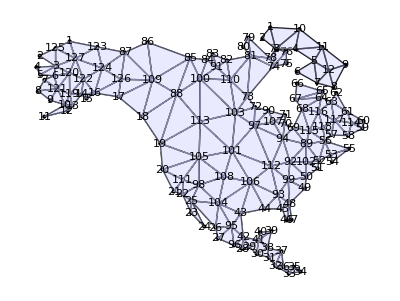

```mathematica
Show[Show2Skeleton[naT,{"Vertices"}],Show2Skeleton[bfT,{"Vertices"}]]
```

```mathematica
Show[miller,
Graphics[{Black,Thickness[t],#}]&/@Line/@Loop[vertices],Graphics /@ Table[Text[ToString[i], vertices[[i]]+{8,1} ], {i, Length[vertices]}]]
```

First::normal: Nonatomic expression expected at position 1 in First[p2].

Append::normal: Nonatomic expression expected at position 1 in Append[p2,First[p2]].

Show::gcomb: Could not combine the graphics objects in Show[Image[Join[ImageData[$Failed]⟦1;;All,1;;1915⟧,ImageData[$Failed]⟦1;;All,6;;86⟧,2]],Append[],{}].

Show[Image[Join[ImageData[$Failed]⟦1;;All,1;;1915⟧,ImageData[$Failed]⟦1;;All,6;;86⟧,2]],Append[-Graphics-],{}]

```mathematica
t=.001;
Show[miller,
Graphics[{Black,Thickness[t],#}]&/@Line/@Loop[vertices],Graphics /@ Table[Text[ToString[i], ea[[i]]+{8,1} ], {i, Length[vertices]}]]
```

First::normal: Nonatomic expression expected at position 1 in First[p2].

Append::normal: Nonatomic expression expected at position 1 in Append[p2,First[p2]].

Show::gcomb: Could not combine the graphics objects in Show[Image[Join[ImageData[$Failed]⟦1;;All,1;;1915⟧,ImageData[$Failed]⟦1;;All,6;;86⟧,2]],Append[],{}].

Show[Image[Join[ImageData[$Failed]⟦1;;All,1;;1915⟧,ImageData[$Failed]⟦1;;All,6;;86⟧,2]],Append[-Graphics-],{}]

```mathematica
region=BoundaryMeshRegion[verticesBase,
Line[Append[Range[Length[verticesBase]],1]]];
T=Triangulate[region,{}];
```

BoundaryMeshRegion::bdcoord: The coordinates given at position 1 in BoundaryMeshRegion[verticesBase,Line[{1}]] are not a list of real-valued points in the same dimension.

Triangulate::aCuteNotFound: The aCute program was not found

```mathematica
eaTOld=eaT;
```

```mathematica
eaT[[1,171]]
```

{1348,973}

```mathematica
eaT[[1,171]]={1348,973};
```

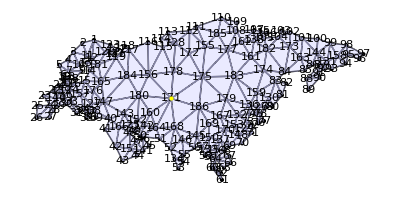

```mathematica
Show[Show2Skeleton[eaT,{"Vertices"}],Graphics[{Yellow,Point[eaT[[1,171]] ]}]]
```